Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario C: high water influx, water_in=750

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
win=750;
ws=alpha*(win-beta);
wt= win-ws;
```

Define system without fire effects:

```mathematica
hdot[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
wdot[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Nullclines and fixed points:

```mathematica
hnull=Simplify[Solve[hdot[H,W]==0,H]]
hnulleq=hnull[[All,1,2]];
hnull1=hnulleq[[1]];
hnull2=hnulleq[[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→453.333-0.6 W}}

```mathematica
wnull=Simplify[Solve[wdot[H,W]==0,H]]
wnulleq=wnull[[All,1,2]];
wnull1=wnulleq[[1]];
(*wnull2=wnulleq[[2]];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→(40500.+382.5 W-0.6 W^2)/(-225.+W)}}

```mathematica
fp=Simplify[Solve[hdot[H,W]==0 && wdot[H,W]==0,{W,H}]]
fpnum=Transpose[{fp[[All,1]][[All,2]],fp[[All,2]][[All,2]]}];
fp1=fpnum[[1]]
fp2=fpnum[[2]]
fp3=fpnum[[3]]
(*fp4=fpnum[[4]]*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→-92.4696,H→0.},{W→692.308,H→37.9487},{W→729.97,H→0.}}

{-92.4696,0.}

{692.308,37.9487}

{729.97,0.}

Plot things

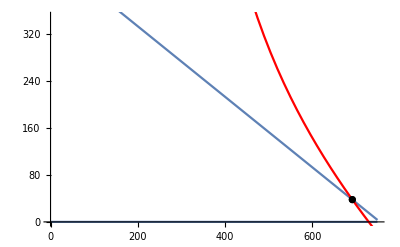

```mathematica
ph1=Plot[hnull1,{W,0,750}];
ph2=Plot[hnull2,{W,0,750}];
pw1=Plot[wnull1,{W,0,750},PlotStyle->Red];
(*pw2=Plot[wnull2,{W,0,750},PlotStyle->Red];*)
points=ListPlot[{fp2},PlotStyle->Black];
Show[ph1,ph2,pw1,points,PlotRange->{0,350}]
```

Jacobian evaluated at second fixed point

```mathematica
j11=D[dhdt[H,W],H]/.fp2;
j12=D[dhdt[H,W],W]/.fp2;
j21=D[dwdt[H,W],H]/.fp2;
j22=D[dhdt[H,W],W]/.fp2;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{-0.0555994,0.}

Jacobian evaluated at third fixed point

```mathematica
j11=D[dhdt[H,W],H]/.fp3;
j12=D[dhdt[H,W],W]/.fp3;
j21=D[dwdt[H,W],H]/.fp3;
j22=D[dhdt[H,W],W]/.fp3;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{0.113538+0.173622 ⅈ,0.113538-0.173622 ⅈ}